```mathematica
Clear["Global`*"]
```

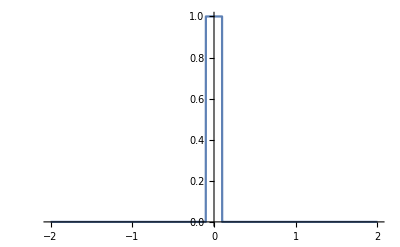

```mathematica
f = HeavisideTheta[x/L+1/10] - HeavisideTheta[x/L-1/10];
Plot[f /. L-> 1,{x,-2,2}]
```

```mathematica
$Assumptions = L >0 && n ∈ Integers && k > 0 && λ >0 && R >0;
```

```mathematica
an = 1/L Integrate[f Cos[(n π x)/L],{x,0,2L}]//FullSimplify
```

Sin[(n π)/10]/(n π)

```mathematica
ψ0c = 2/20+2Sum[an Cos[(n π x)/L],{n,1,100}];
```

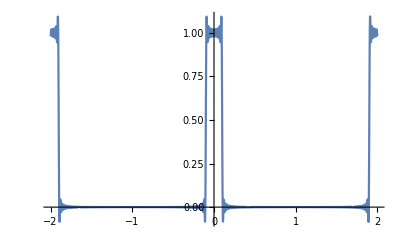

```mathematica
Plot[ψ0c/.L-> 1,{x,-2,2},PlotRange->Full]
```

```mathematica
ψS = Exp[-I k R](1/2 + 2Sum[an Exp[(I π R λ n^2)/L^2] Cos[(n π x)/L],{n,1,100}])/. L-> 1 /. λ-> 10^-3 ;
```

```mathematica
DensityPlot[Abs[ψS]^2//Simplify,{x,-5,5},{R,0,2000},PlotPoints->400,MaxRecursion->2,ColorFunction->"Rainbow",PlotRange->Full,MaxRecursion->2]
```

-Graphics-